```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]

(*Define the initial state*)initialState=Ket[1];

(*Define the rotation around the y-axis*)
theta=Pi/4; (*Example angle-change as desired*)
rotationMatrix={{Cos[theta/2],-Sin[theta/2]},{Sin[theta/2],Cos[theta/2]}};

(*Apply the rotation to the state*)
finalState=rotationMatrix.initialState;

(*Convert quantum state to Bloch vector*)

stateToBlochVector[state_]:={
2 Re[state[[1]] Conjugate[state[[2]]]],
2 Im[state[[2]] Conjugate[state[[1]]]],
Abs[state[[1]]]^2-Abs[state[[2]]]^2
};

initialVector={0,0,1};
finalVector=stateToBlochVector[finalState];

(*Plotting*)
Graphics3D[{{Opacity[0.5],Sphere[{0,0,0},1]},(*Bloch Sphere*){Red,Arrow[{{0,0,0},initialVector}]},(*Initial State*){Blue,Arrow[{{0,0,0},finalVector}]} (*Final State*)},Axes->True,AxesLabel->{"x","y","z"},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Lighting->"Neutral",PlotLabel->"Bloch Sphere Representation"]
```

PacletObject[…]

-Graphics3D-

```mathematica
(*Define the function*)f[u_,n_]:=(1/Factorial[n]) Exp[-u^2] u^(2 n)

(*Define beta as an arbitrary constant*)
beta=1+5*I;

(*Define the plot function*)
ComplexPlot3D[f[Abs[z-beta],36],{z,-10-10 I,10+10 I},PlotRange->All,AxesLabel->{"Re[α]","Im[α]","f"},PlotLabel->"Function plot in complex plane"]
```

-Graphics3D-

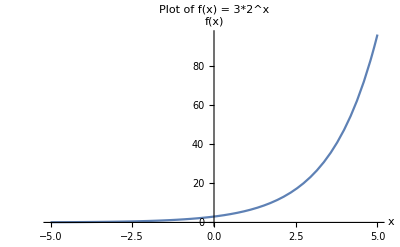

```mathematica
f[x_]:=3*2^x

(*Plot the function for x in the range from-5 to 5 as an example*)
Plot[f[x],{x,-5,5},PlotRange->All,AxesLabel->{"x","f(x)"},LabelStyle->Directive[Bold,Black],PlotLabel->"Plot of f(x) = 3*2^x"]
```